```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.5,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→0.5,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

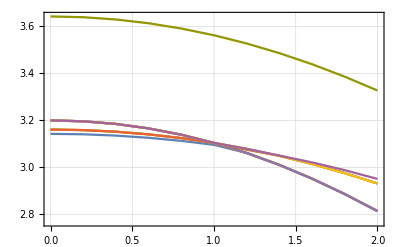

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

1.30848×10^-18

1

0.000165128

1

0.000660994

1

0.00148902

1

0.00265153

1

0.00415164

1

0.00599315

1

0.00818036

1

0.0107179

1

0.0136104

1

0.0168625

1

5.80159

1

5.76219

1

5.71955

1

5.67402

1

5.62601

1

5.576

1

5.52448

1

5.47199

1

5.41901

1

5.36601

2

2.

2

1.99982

2

1.99929

2

1.9984

2

1.99714

2

1.9955

2

1.99348

2

1.99104

2

1.98818

2

1.98488

2

1.9811

2

5.80159

2

5.76219

2

5.71955

2

5.67402

2

5.62601

2

5.576

2

5.52448

2

5.47199

2

5.41901

2

5.36601

3

2.

3

1.99982

3

1.99929

3

1.9984

3

1.99714

3

1.9955

3

1.99348

3

1.99104

3

1.98818

3

1.98488

3

1.9811

3

5.80159

3

5.76219

3

5.71955

3

5.67402

3

5.62601

3

5.576

3

5.52448

3

5.47199

3

5.41901

3

5.36601

4

2.

4

1.99982

4

1.99929

4

1.9984

4

1.99714

4

1.9955

4

1.99348

4

1.99104

4

1.98818

4

1.98488

4

1.9811

4

5.80159

4

5.76219

4

5.71955

4

5.67402

4

5.62601

4

5.576

4

5.52448

4

5.47199

4

5.41901

4

5.36601

5

6.

5

5.9985

5

5.99399

5

5.98641

5

5.97564

5

5.96157

5

5.94407

5

5.92299

5

5.89823

5

5.86973

5

5.83749

5

5.80159

5

5.76219

5

5.71955

5

5.67402

5

5.62601

5

5.576

5

5.52448

5

5.47199

5

5.41901

5

5.36601

6

6.

6

5.9985

6

5.99399

6

5.98641

6

5.97564

6

5.96157

6

5.94407

6

5.92299

6

5.89823

6

5.86973

6

5.83749

6

0.020478

6

0.02446

6

0.0288104

6

1.96085

6

1.95438

6

1.94729

6

1.93956

6

1.93118

6

1.92213

6

1.91239

7

6.

7

5.9985

7

5.99399

7

5.98641

7

5.97564

7

5.96157

7

5.94407

7

5.92299

7

5.89823

7

5.86973

7

5.83749

7

1.97684

7

1.97206

7

1.96674

7

1.96085

7

1.95438

7

1.94729

7

1.93956

7

1.93118

7

1.92213

7

1.91239

8

6.

8

5.9985

8

5.99399

8

5.98641

8

5.97564

8

5.96157

8

5.94407

8

5.92299

8

5.89823

8

5.86973

8

5.83749

8

1.97684

8

1.97206

8

1.96674

8

1.96085

8

1.95438

8

1.94729

8

1.93956

8

1.93118

8

1.92213

8

1.91239

9

6.

9

5.9985

9

5.99399

9

5.98641

9

5.97564

9

5.96157

9

5.94407

9

5.92299

9

5.89823

9

5.86973

9

5.83749

9

1.97684

9

1.97206

9

1.96674

9

0.0335294

9

0.0386152

9

0.0440636

9

0.0498677

9

0.0560174

9

0.0624995

9

0.0692971

10

0.75

10

0.74996

10

0.749839

10

0.74964

10

0.749363

10

0.749012

10

0.74859

10

0.748102

10

0.747551

10

0.746943

10

0.746283

10

0.745577

10

0.744831

10

0.744052

10

0.743245

10

0.742418

10

0.741576

10

0.740725

10

0.739872

10

0.739023

10

0.738182

```mathematica
data1//MatrixForm
```

(1 | 0. | 1.30848×10^-18 | 3.1428
1 | 0.1 | 0.000165128 | 3.14234
1 | 0.2 | 0.000660994 | 3.14095
1 | 0.3 | 0.00148902 | 3.13862
1 | 0.4 | 0.00265153 | 3.13537
1 | 0.5 | 0.00415164 | 3.13118
1 | 0.6 | 0.00599315 | 3.12605
1 | 0.7 | 0.00818036 | 3.11997
1 | 0.8 | 0.0107179 | 3.11294
1 | 0.9 | 0.0136104 | 3.10494
1 | 1. | 0.0168625 | 3.09597
1 | 1.1 | 5.80159 | 3.08384
1 | 1.2 | 5.76219 | 3.06139
1 | 1.3 | 5.71955 | 3.03696
1 | 1.4 | 5.67402 | 3.01056
1 | 1.5 | 5.62601 | 2.98223
1 | 1.6 | 5.576 | 2.95204
1 | 1.7 | 5.52448 | 2.92004
1 | 1.8 | 5.47199 | 2.88631
1 | 1.9 | 5.41901 | 2.85091
1 | 2. | 5.36601 | 2.81395
2 | 0. | 2. | 3.16104
2 | 0.1 | 1.99982 | 3.16047
2 | 0.2 | 1.99929 | 3.15877
2 | 0.3 | 1.9984 | 3.15594
2 | 0.4 | 1.99714 | 3.15198
2 | 0.5 | 1.9955 | 3.14688
2 | 0.6 | 1.99348 | 3.14064
2 | 0.7 | 1.99104 | 3.13326
2 | 0.8 | 1.98818 | 3.12472
2 | 0.9 | 1.98488 | 3.11504
2 | 1. | 1.9811 | 3.1042
2 | 1.1 | 5.80159 | 3.08384
2 | 1.2 | 5.76219 | 3.06139
2 | 1.3 | 5.71955 | 3.03696
2 | 1.4 | 5.67402 | 3.01056
2 | 1.5 | 5.62601 | 2.98223
2 | 1.6 | 5.576 | 2.95204
2 | 1.7 | 5.52448 | 2.92004
2 | 1.8 | 5.47199 | 2.88631
2 | 1.9 | 5.41901 | 2.85091
2 | 2. | 5.36601 | 2.81395
3 | 0. | 2. | 3.16104
3 | 0.1 | 1.99982 | 3.16047
3 | 0.2 | 1.99929 | 3.15877
3 | 0.3 | 1.9984 | 3.15594
3 | 0.4 | 1.99714 | 3.15198
3 | 0.5 | 1.9955 | 3.14688
3 | 0.6 | 1.99348 | 3.14064
3 | 0.7 | 1.99104 | 3.13326
3 | 0.8 | 1.98818 | 3.12472
3 | 0.9 | 1.98488 | 3.11504
3 | 1. | 1.9811 | 3.1042
3 | 1.1 | 5.80159 | 3.08384
3 | 1.2 | 5.76219 | 3.06139
3 | 1.3 | 5.71955 | 3.03696
3 | 1.4 | 5.67402 | 3.01056
3 | 1.5 | 5.62601 | 2.98223
3 | 1.6 | 5.576 | 2.95204
3 | 1.7 | 5.52448 | 2.92004
3 | 1.8 | 5.47199 | 2.88631
3 | 1.9 | 5.41901 | 2.85091
3 | 2. | 5.36601 | 2.81395
4 | 0. | 2. | 3.16104
4 | 0.1 | 1.99982 | 3.16047
4 | 0.2 | 1.99929 | 3.15877
4 | 0.3 | 1.9984 | 3.15594
4 | 0.4 | 1.99714 | 3.15198
4 | 0.5 | 1.9955 | 3.14688
4 | 0.6 | 1.99348 | 3.14064
4 | 0.7 | 1.99104 | 3.13326
4 | 0.8 | 1.98818 | 3.12472
4 | 0.9 | 1.98488 | 3.11504
4 | 1. | 1.9811 | 3.1042
4 | 1.1 | 5.80159 | 3.08384
4 | 1.2 | 5.76219 | 3.06139
4 | 1.3 | 5.71955 | 3.03696
4 | 1.4 | 5.67402 | 3.01056
4 | 1.5 | 5.62601 | 2.98223
4 | 1.6 | 5.576 | 2.95204
4 | 1.7 | 5.52448 | 2.92004
4 | 1.8 | 5.47199 | 2.88631
4 | 1.9 | 5.41901 | 2.85091
4 | 2. | 5.36601 | 2.81395
5 | 0. | 6. | 3.2
5 | 0.1 | 5.9985 | 3.19906
5 | 0.2 | 5.99399 | 3.19625
5 | 0.3 | 5.98641 | 3.19154
5 | 0.4 | 5.97564 | 3.18494
5 | 0.5 | 5.96157 | 3.17641
5 | 0.6 | 5.94407 | 3.16595
5 | 0.7 | 5.92299 | 3.15352
5 | 0.8 | 5.89823 | 3.13911
5 | 0.9 | 5.86973 | 3.1227
5 | 1. | 5.83749 | 3.10427
5 | 1.1 | 5.80159 | 3.08384
5 | 1.2 | 5.76219 | 3.06139
5 | 1.3 | 5.71955 | 3.03696
5 | 1.4 | 5.67402 | 3.01056
5 | 1.5 | 5.62601 | 2.98223
5 | 1.6 | 5.576 | 2.95204
5 | 1.7 | 5.52448 | 2.92004
5 | 1.8 | 5.47199 | 2.88631
5 | 1.9 | 5.41901 | 2.85091
5 | 2. | 5.36601 | 2.81395
6 | 0. | 6. | 3.2
6 | 0.1 | 5.9985 | 3.19906
6 | 0.2 | 5.99399 | 3.19625
6 | 0.3 | 5.98641 | 3.19154
6 | 0.4 | 5.97564 | 3.18494
6 | 0.5 | 5.96157 | 3.17641
6 | 0.6 | 5.94407 | 3.16595
6 | 0.7 | 5.92299 | 3.15352
6 | 0.8 | 5.89823 | 3.13911
6 | 0.9 | 5.86973 | 3.1227
6 | 1. | 5.83749 | 3.10427
6 | 1.1 | 0.020478 | 3.08603
6 | 1.2 | 0.02446 | 3.07509
6 | 1.3 | 0.0288104 | 3.06315
6 | 1.4 | 1.96085 | 3.0492
6 | 1.5 | 1.95438 | 3.03252
6 | 1.6 | 1.94729 | 3.01467
6 | 1.7 | 1.93956 | 2.99563
6 | 1.8 | 1.93118 | 2.97543
6 | 1.9 | 1.92213 | 2.95405
6 | 2. | 1.91239 | 2.9315
7 | 0. | 6. | 3.2
7 | 0.1 | 5.9985 | 3.19906
7 | 0.2 | 5.99399 | 3.19625
7 | 0.3 | 5.98641 | 3.19154
7 | 0.4 | 5.97564 | 3.18494
7 | 0.5 | 5.96157 | 3.17641
7 | 0.6 | 5.94407 | 3.16595
7 | 0.7 | 5.92299 | 3.15352
7 | 0.8 | 5.89823 | 3.13911
7 | 0.9 | 5.86973 | 3.1227
7 | 1. | 5.83749 | 3.10427
7 | 1.1 | 1.97684 | 3.0922
7 | 1.2 | 1.97206 | 3.07904
7 | 1.3 | 1.96674 | 3.0647
7 | 1.4 | 1.96085 | 3.0492
7 | 1.5 | 1.95438 | 3.03252
7 | 1.6 | 1.94729 | 3.01467
7 | 1.7 | 1.93956 | 2.99563
7 | 1.8 | 1.93118 | 2.97543
7 | 1.9 | 1.92213 | 2.95405
7 | 2. | 1.91239 | 2.9315
8 | 0. | 6. | 3.2
8 | 0.1 | 5.9985 | 3.19906
8 | 0.2 | 5.99399 | 3.19625
8 | 0.3 | 5.98641 | 3.19154
8 | 0.4 | 5.97564 | 3.18494
8 | 0.5 | 5.96157 | 3.17641
8 | 0.6 | 5.94407 | 3.16595
8 | 0.7 | 5.92299 | 3.15352
8 | 0.8 | 5.89823 | 3.13911
8 | 0.9 | 5.86973 | 3.1227
8 | 1. | 5.83749 | 3.10427
8 | 1.1 | 1.97684 | 3.0922
8 | 1.2 | 1.97206 | 3.07904
8 | 1.3 | 1.96674 | 3.0647
8 | 1.4 | 1.96085 | 3.0492
8 | 1.5 | 1.95438 | 3.03252
8 | 1.6 | 1.94729 | 3.01467
8 | 1.7 | 1.93956 | 2.99563
8 | 1.8 | 1.93118 | 2.97543
8 | 1.9 | 1.92213 | 2.95405
8 | 2. | 1.91239 | 2.9315
9 | 0. | 6. | 3.2
9 | 0.1 | 5.9985 | 3.19906
9 | 0.2 | 5.99399 | 3.19625
9 | 0.3 | 5.98641 | 3.19154
9 | 0.4 | 5.97564 | 3.18494
9 | 0.5 | 5.96157 | 3.17641
9 | 0.6 | 5.94407 | 3.16595
9 | 0.7 | 5.92299 | 3.15352
9 | 0.8 | 5.89823 | 3.13911
9 | 0.9 | 5.86973 | 3.1227
9 | 1. | 5.83749 | 3.10427
9 | 1.1 | 1.97684 | 3.0922
9 | 1.2 | 1.97206 | 3.07904
9 | 1.3 | 1.96674 | 3.0647
9 | 1.4 | 0.0335294 | 3.05021
9 | 1.5 | 0.0386152 | 3.03625
9 | 1.6 | 0.0440636 | 3.02126
9 | 1.7 | 0.0498677 | 3.00524
9 | 1.8 | 0.0560174 | 2.98818
9 | 1.9 | 0.0624995 | 2.97008
9 | 2. | 0.0692971 | 2.95092
10 | 0. | 0.75 | 3.64267
10 | 0.1 | 0.74996 | 3.64186
10 | 0.2 | 0.749839 | 3.63945
10 | 0.3 | 0.74964 | 3.63542
10 | 0.4 | 0.749363 | 3.62979
10 | 0.5 | 0.749012 | 3.62257
10 | 0.6 | 0.74859 | 3.61374
10 | 0.7 | 0.748102 | 3.60332
10 | 0.8 | 0.747551 | 3.59132
10 | 0.9 | 0.746943 | 3.57774
10 | 1. | 0.746283 | 3.56259
10 | 1.1 | 0.745577 | 3.54588
10 | 1.2 | 0.744831 | 3.52763
10 | 1.3 | 0.744052 | 3.50784
10 | 1.4 | 0.743245 | 3.48652
10 | 1.5 | 0.742418 | 3.46369
10 | 1.6 | 0.741576 | 3.43936
10 | 1.7 | 0.740725 | 3.41355
10 | 1.8 | 0.739872 | 3.38627
10 | 1.9 | 0.739023 | 3.35754
10 | 2. | 0.738182 | 3.32737)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;11,1;;4]];
tmp02 = data1[[117;;119,1;;4]];
tmp03 = data1[[183;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;32,1;;4]];
tmp02 = data1[[180;;182, 1;;4]];
tmp03 = data1[[120;;126, 1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e1data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.1428 | 1.30848×10^-18
0.1 | 3.14234 | 0.000165128
0.2 | 3.14095 | 0.000660994
0.3 | 3.13862 | 0.00148902
0.4 | 3.13537 | 0.00265153
0.5 | 3.13118 | 0.00415164
0.6 | 3.12605 | 0.00599315
0.7 | 3.11997 | 0.00818036
0.8 | 3.11294 | 0.0107179
0.9 | 3.10494 | 0.0136104
1. | 3.09597 | 0.0168625
1.1 | 3.08603 | 0.020478
1.2 | 3.07509 | 0.02446
1.3 | 3.06315 | 0.0288104
1.4 | 3.05021 | 0.0335294
1.5 | 3.03625 | 0.0386152
1.6 | 3.02126 | 0.0440636
1.7 | 3.00524 | 0.0498677
1.8 | 2.98818 | 0.0560174
1.9 | 2.97008 | 0.0624995
2. | 2.95092 | 0.0692971)

(0. | 3.16104 | 2.
0.1 | 3.16047 | 1.99982
0.2 | 3.15877 | 1.99929
0.3 | 3.15594 | 1.9984
0.4 | 3.15198 | 1.99714
0.5 | 3.14688 | 1.9955
0.6 | 3.14064 | 1.99348
0.7 | 3.13326 | 1.99104
0.8 | 3.12472 | 1.98818
0.9 | 3.11504 | 1.98488
1. | 3.1042 | 1.9811
1.1 | 3.0922 | 1.97684
1.2 | 3.07904 | 1.97206
1.3 | 3.0647 | 1.96674
1.4 | 3.0492 | 1.96085
1.5 | 3.03252 | 1.95438
1.6 | 3.01467 | 1.94729
1.7 | 2.99563 | 1.93956
1.8 | 2.97543 | 1.93118
1.9 | 2.95405 | 1.92213
2. | 2.9315 | 1.91239)

(0. | 3.2 | 6.
0.1 | 3.19906 | 5.9985
0.2 | 3.19625 | 5.99399
0.3 | 3.19154 | 5.98641
0.4 | 3.18494 | 5.97564
0.5 | 3.17641 | 5.96157
0.6 | 3.16595 | 5.94407
0.7 | 3.15352 | 5.92299
0.8 | 3.13911 | 5.89823
0.9 | 3.1227 | 5.86973
1. | 3.10427 | 5.83749
1.1 | 3.08384 | 5.80159
1.2 | 3.06139 | 5.76219
1.3 | 3.03696 | 5.71955
1.4 | 3.01056 | 5.67402
1.5 | 2.98223 | 5.62601
1.6 | 2.95204 | 5.576
1.7 | 2.92004 | 5.52448
1.8 | 2.88631 | 5.47199
1.9 | 2.85091 | 5.41901
2. | 2.81395 | 5.36601)

```mathematica
|
```

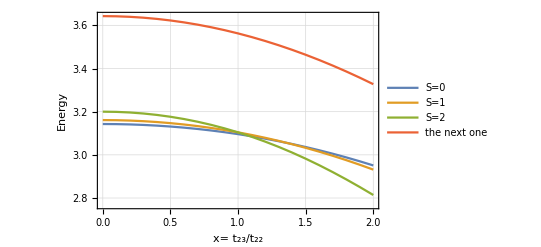

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

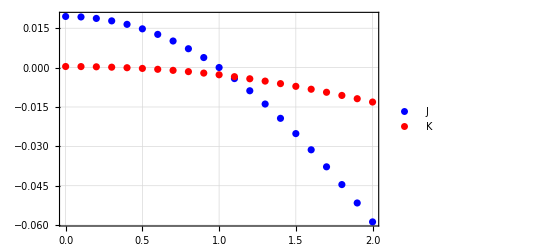

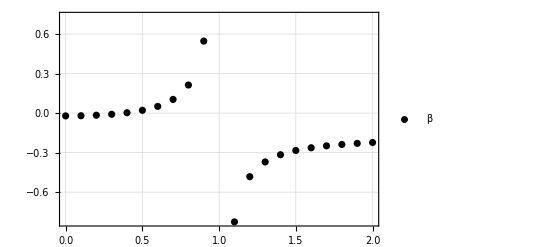

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```